```mathematica
Clear["Global`*"]
```

## All of the following is for a kappa dist(!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!!)

```mathematica
phiBarK[phiBar_,kappa_]:=phiBar/(kappa-3/2)
```

```mathematica
Integrand[kappa_,t_]:=t^(kappa-3/2)(1-t)^(1/2)
```

```mathematica
Aich1[u1_,u2_,kappa_]:=NIntegrate[t^(kappa-3/2)(1-t)^(1/2),{t,u1,u2},WorkingPrecision->18]
```

```mathematica
Aich1Ancho[u1_,u2_,kappa_,ancillary_]:=NIntegrate[ancillary*t^(kappa-3/2)(1-t)^(1/2),{t,u1,u2},WorkingPrecision->18]
```

Original

```mathematica
(*densFacK[phiBarK_,kappa_,RB_]:=1/2 Gamma[kappa+1]/(Gamma[3/2]Gamma[kappa-1/2])( (1-RB-phiBarK)^(1/2)(1+phiBarK/(RB-1))^-kappa Aich1[1/(1+RB)(1-RB/(1-phiBarK)),(1-RB-phiBarK)/((1+RB)(1+phiBarK/(RB-1))),kappa]+1/(1-phiBarK)^(kappa-1/2)Aich1[0,1-phiBarK,kappa]);*)
```

Try #2: replace first argument of Aich1 with something possibly simpler, which also matches the outside: 1/(1+RB)(1-RB/(1-phiBarK))-> (1-RB-phiBarK)/((1+RB)(1-phiBarK))
(For the record, this version is definitely illegal. The replacement (1-RB-phiBarK)/((1+RB)(1+phiBarK/(RB-1)))=(1-RB-phiBarK)/(1+RB+phiBarK) is bogus!!

```mathematica
(*densFacK[phiBarK_,kappa_,RB_]:=1/2 Gamma[kappa+1]/(Gamma[3/2]Gamma[kappa-1/2])( (1-RB-phiBarK)^(1/2)(1+phiBarK/(RB-1))^-kappa Aich1[(1-RB-phiBarK)/((1+RB)(1-phiBarK)),(1-RB-phiBarK)/(1+RB+phiBarK),kappa]+1/(1-phiBarK)^(kappa-1/2)Aich1[0,1-phiBarK,kappa])*)
```

Still not working ...

#### Try this way

```mathematica
densFacK[phiBarK_,kappa_,RB_]:=1/2 Gamma[kappa+1]/(Gamma[3/2]Gamma[kappa-1/2])( (1-RB)^kappa/(1-RB-phiBarK)^(kappa-1/2)Aich1[1/(1+RB)(1-RB/(1-phiBarK)),(1-RB)/(1+RB),kappa]+Aich1[0,1-phiBarK,kappa]/(1-phiBarK)^(kappa-1/2));
```

```mathematica
densFacKAncho[phiBarK_,kappa_,RB_]:=1/2 Gamma[kappa+1]/(Gamma[3/2]Gamma[kappa-1/2])( Aich1Ancho[1/(1+RB)(1-RB/(1-phiBarK)),(1-RB)/(1+RB),kappa,(1-RB)^kappa/(1-RB-phiBarK)^(kappa-1/2)]+Aich1Ancho[0,1-phiBarK,kappa,(1-phiBarK)^(kappa-1/2)]);
```

#### Chunked-out parts of the densFacK function

```mathematica
part1[phiBarK_,kappa_,RB_]:=(1-RB)^kappa/(1-RB-phiBarK)^(kappa-1/2)
H1p1[phiBarK_,kappa_,RB_]:=Aich1[1/(1+RB)(1-RB/(1-phiBarK)),(1-RB-phiBarK)/((1+RB)(1+phiBarK/(RB-1))),kappa]
```

```mathematica
part2[phiBarK_,kappa_,RB_]:=1/(1-phiBarK)^(kappa-1/2)
H1p2[phiBarK_,kappa_,RB_]:=Aich1[0,1-phiBarK,kappa]
```

### z_(1,2(α=1))^* and z_(1(α=1)) —see equations (30) in Liemohn and Khazanov [1998]

```mathematica
zStar11[phiBarK_,RB_]:=1/(1+RB)(1-RB/(1-phiBarK))
zStar21[RB_]:=(1-RB)/(1+RB)
z11[phiBarK_]:=1-phiBarK
```

```mathematica
Plot3D[zStar11[a,b],{a,-6.,6.},{b,-6.,6.}]
```

-Graphics3D-

```mathematica
kappa=5;
```

```mathematica
dPhi=941;
```

```mathematica
T=110;
```

```mathematica
N[dPhi/T]
```

8.55455

```mathematica
RB=10;
```

```mathematica
phiBarK[dPhi/T,100]
```

941/10835

```mathematica
plotLimzStar1:={All,{-10,10}};
```

```mathematica
dPhiManipList:={1,3,10,30,100,300,1000,3000,10000,30000};
phiBarManipList:={1,3,10,30,100,300,1000,3000,10000,30000};
RBManipList:={1,3,10,30,100,300,1000,3000,10000,1*^5,1*^6,∞};
RBInit=72;
```

#### Plot z_(1(α=1))^*((ϕ̄)_κ,RB)

```mathematica
(*zStar11String[dPhi_,T_,RB_]:=StringForm["z_(1(α = 1))^* for ΔΦ = `1`, T = `2` eV, R_B = `3`",dPhi,T,RB];*)
zStar11String[phiBar_,RB_]:=StringForm["z_(1 (α = 1))^* for ϕ̄ = `1`, R_B = `2`",phiBar,RB]
```

```mathematica
Manipulate[LogLinearPlot[FullSimplify[zStar11[phiBarK[phiBar,kappa],RB]],{kappa,1.5,1000},PlotRange->plotLimzStar1,Frame->True,FrameLabel->{"κ","z_(1 (α = 1))^*"},FrameStyle->(FontSize->18),Epilog->{Text[Style[zStar11String[phiBar,RB],18],Scaled[{0.5,0.9}],{0,0}]},ImageSize->700],{{RB,RBInit},RBManipList},{{phiBar,dPhi/T},1,40}]
```

#### Plot z_(2(α=1))^*(RB)

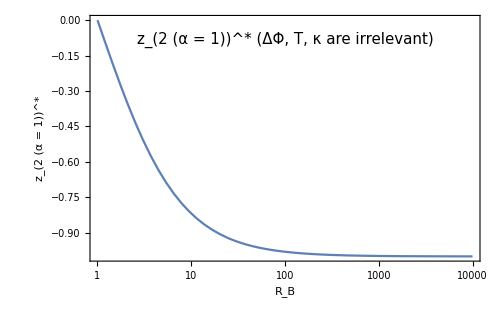

```mathematica
LogLinearPlot[zStar21[RB],{RB,1,10000},PlotRange->{All,Full},Frame->True,FrameLabel->{"R_B","z_(2 (α = 1))^*"},FrameStyle->(FontSize->17),Epilog->{Text[Style[StringForm["z_(2 (α = 1))^* (ΔΦ, T, κ are irrelevant)"],15],Scaled[{0.5,0.9}],{0,0}]},ImageSize->500]
```

#### Plot z_(2(α=1))^*(RB)-z_(1(α=1))^*((ϕ̄)_κ,RB)

```mathematica
Manipulate[LogLinearPlot[zStar21[RB]-zStar11[phiBarK[phiBar,kappa],RB],{kappa,1.5,100},PlotRange->{All,Automatic},Frame->True,FrameLabel->{"κ","z_(2 (α = 1))^*-z_(1 (α = 1))^*"},FrameStyle->(FontSize->17),Epilog->{Text[Style[StringForm["ϕ̄ = `1`, R_B = `2`",phiBar,RB],15],Scaled[{0.97,0.97}],{1,1}]},ImageSize->600],{{RB,RBInit},RBManipList},{{phiBar,dPhi/T},1,40}]
```

```mathematica
Manipulate[LogLogPlot[phiBarK[phiBar,kappa],{kappa,3/2,100},ImageSize->600,Frame->True,FrameLabel->{κ,StringForm["ϕ̄(κ)"]},FrameStyle->(FontSize->17),Epilog->{Text[Style[StringForm["(ϕ̄)_κ for ϕ̄ = `1`",phiBar],16],Scaled[{0.97,0.97}],{1,1}]}],{{phiBar,dPhi/T},1,40}]
```

```mathematica
kappa=20
```

20

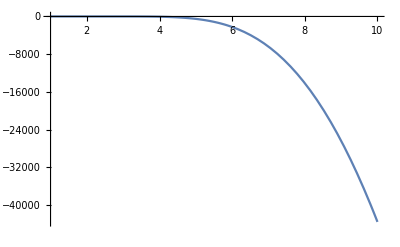

```mathematica
Plot[densFacKAncho[phiBarK[dPhi/T,kappa],kappa,RB],{RB,1,10}]
```

```mathematica
densFacK[phiBarK[dPhi/T,kappa],kappa,RB]
```

-3.610231686680072×10^8

```mathematica
densFacKAncho[phiBarK[dPhi/T,kappa],kappa,RB]
```

-0.00041922901799508028